```mathematica
ℏ=1.0*10^-34;
kb=1.38*10^-23;
T0=6.4*10^-6;
m171=170.936*(1.660539*10^-27);
```

```mathematica
ωt=2π 10.^5;
```

```mathematica
Pn[n_,T_]:=E^(-ℏ ωt n/(kb T))(1-E^(-ℏ ωt/(kb T)))
T[nbar_]:=(ℏ ωt)/(kb Log[1/nbar+1])
```

```mathematica
(-ℏ (134*10^3))/(kb Log[1.6/2.6])
```

2.×10^-6

```mathematica
(-ℏ (24*10^3))/(kb Log[6/(1+6)])
```

1.1282×10^-6

```mathematica
Solve[E^(-ℏ ω n/(kb T))(1-E^(-ℏ ω/(kb T)))]
```

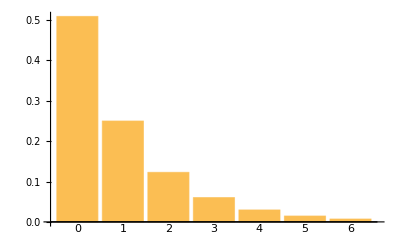

```mathematica
BarChart[Table[Pn[n,T0],{n,0,6}],ChartLabels->{"0","1","2","3","4","5","6"}]
```

## adiabatic transfer lamb dicke limit

```mathematica
Ht[t_]:=({{ωe/2+Δs((2*t)/Tp-1)+Δ0, Ω/2}, {Ω/2, ωg/2}});
MatrixForm[Ht[t]]
```

(Δ0+(-1+(2 t)/Tp) Δs+ωe/2 | Ω/2
Ω/2 | ωg/2)

```mathematica
Ttot=100./(5*10^4)
```

0.002

```mathematica
Htn[t_]:=Ht[t]/.{ωe->ωt/2,ωg->ωt,Ω->5.*10^4,Δ0->ωt/4,Δs->ωt,Tp->Ttot,η->η0};
ψs=NDSolve[{I ψ'[t]==Htn[t].ψ[t],ψ[0]=={0,1}},ψ,{t,0,Ttot}]
```

{{ψ→InterpolatingFunction[{{0., 0.002}}, <>]}}

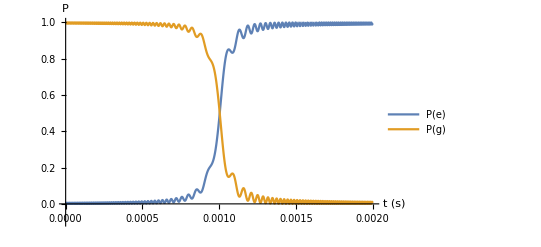

```mathematica
Plot[{Abs[Evaluate[ψ[t]/.ψs][[1,1]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,2]]]^2},{t,0,Ttot},PlotRange->{-0.1,1},AxesLabel->{"t (s)","P"},PlotLegends->{"P(e)","P(g)"}]
```

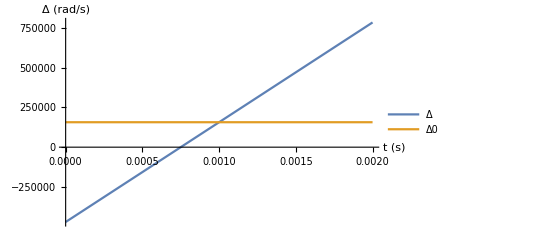

```mathematica
Plot[{(Δs((2*t)/Tp-1)+Δ0)/.{Δ0->ωt/4,Δs->ωt,Tp->Ttot},ωt/4},{t,0,Ttot},PlotLegends->{"Δ","Δ0"},AxesLabel->{"t (s)","Δ (rad/s)"}]
```

## motional overlap different trap freq

```mathematica
ψn[x_,y_,z_,n_,ω_]:=1/((2^n(n!))^(3/2)) Exp[-1/(2 ℏ)m171 ω (x^2+y^2+z^2)]HermiteH[n,√((m171 ω)/ℏ)x]HermiteH[n,√((m171 ω)/ℏ)y]HermiteH[n,√((m171 ω)/ℏ)z]
ψn1D[x_,n_,ω_]:=1/((2^n(n!))^(1/2))((m171 ω)/(π ℏ))^(1/4)Exp[-1/(2 ℏ)m171 ω (x^2)]HermiteH[n,√((m171 ω)/ℏ)x]
```

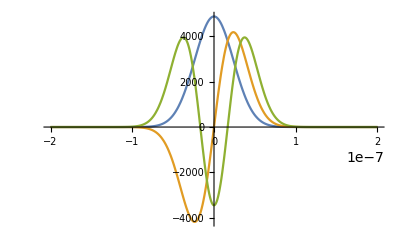

```mathematica
Plot[{ψn1D[x,0,ωt],ψn1D[x,1,ωt],ψn1D[x,2,ωt]},{x,-200*10^-9,200*10^-9},PlotRange->All]
```

```mathematica
Plot3D[ψn[x,y,0,2,ωt],{x,-1*10^-7,1*10^-7},{y,-1*10^-7,1*10^-7},PlotRange->All]
```

-Graphics3D-

```mathematica
ψnN[x_,y_,z_,nx_,ny_,nz_,ω_,m_]:=1/((2^(nx+ny+nz)(nx!)(ny!)(nz!))^(1/2)) ((m ω)/π)^(3/4)Exp[-1/2 m ω (x^2+y^2+z^2)]HermiteH[nx,√(m ω)x]HermiteH[ny,√(m ω)y]HermiteH[nz,√(m ω)z]
```

```mathematica
NIntegrate[ψnN[x,y,z,0,0,0,1.,1.]*ψnN[x,y,z,2,2,2,1/2.,1.],{x,-5,5},{y,-5,5},{z,-5,5},AccuracyGoal->5]
```

-0.0119873

```mathematica
Sum[Abs[NIntegrate[ψnN[x,y,z,0,0,0,1,1]*ψnN[x,y,z,nx,ny,nz,1/2,1],{x,-5,5},{y,-5,5},{z,-5,5},AccuracyGoal->5]]^2,{nx,0,6,2},{ny,0,6,2},{nz,0,6,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.999869

```mathematica
NIntegrate[ψnN[x,y,z,0,0,0,1,1]*ψnN[x,y,z,0,0,0,1/2,1],{x,-5,5},{y,-5,5},{z,-5,5},AccuracyGoal->5]
```

0.915452

```mathematica
T =(ℏ 0.5)/(kb(-Log[(1-0.91545)]))
```

1.46663×10^-12

```mathematica
nbar=0.1;
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
```

```mathematica
Sum[Pns[[n+1]]*n,{n,0,n0}]
```

0.1

```mathematica
Pns
```

{0.909091,0.0826446,0.00751315,0.000683013,0.0000620921,5.64474×10^-6,5.13158×10^-7,4.66507×10^-8,4.24098×10^-9,3.85543×10^-10,3.50494×10^-11,3.18631×10^-12,2.89664×10^-13,2.63331×10^-14,2.39392×10^-15,2.17629×10^-16,1.97845×10^-17,1.79859×10^-18,1.63508×10^-19,1.48644×10^-20,1.35131×10^-21}

## H form

```mathematica
n0=3;
Hs0=({{-1/2 δ, 0}, {0, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ωe, 0}, {0, ωg}})];
a=DiagonalMatrix[Table[√(n0-n),{n,0,n0}]];
For[i=n0,i>0,i--,
a=Permute[a,Cycles[{{i,i+1}}]]
]
Hcsge=Ω/2({{0, 1}, {0, 0}});
Hcmge=IdentityMatrix[n0+1]+Sum[(I η)^n/(n!)MatrixPower[(a+a†),n],{n,1,6}];
Hcge=KroneckerProduct[Hcmge,Hcsge];
Hc=Hcge+Hcge†;
MatrixForm[Hc];
H=Hs+Hm+Hc;
FullSimplify[MatrixForm[H/.{ωe->ωg,δ->0}],Assumptions->{η∈Reals,Ω∈Reals,ωg∈Reals}]
```

((7 ωg)/2 | 1/160 (80-120 η^2+50 η^4-9 η^6) Ω | 0 | (ⅈ η (120-100 η^2+27 η^4) Ω)/(80 √3) | 0 | -(η^2 (120-60 η^2+11 η^4) Ω)/(80 √6) | 0 | (ⅈ η^3 (-10+3 η^2) Ω)/(20 √6)
1/160 (80-120 η^2+50 η^4-9 η^6) Ω | (7 ωg)/2 | -(ⅈ η (120-100 η^2+27 η^4) Ω)/(80 √3) | 0 | -(η^2 (120-60 η^2+11 η^4) Ω)/(80 √6) | 0 | (ⅈ η^3 (10-3 η^2) Ω)/(20 √6) | 0
0 | (ⅈ η (120-100 η^2+27 η^4) Ω)/(80 √3) | (5 ωg)/2 | 1/2 (1-(5 η^2)/2+(9 η^4)/8-(49 η^6)/240) Ω | 0 | (ⅈ η (40-40 η^2+11 η^4) Ω)/(40 √2) | 0 | -(η^2 (120-60 η^2+11 η^4) Ω)/(240 √2)
-(ⅈ η (120-100 η^2+27 η^4) Ω)/(80 √3) | 0 | 1/480 (240-600 η^2+270 η^4-49 η^6) Ω | (5 ωg)/2 | -(ⅈ η (40-40 η^2+11 η^4) Ω)/(40 √2) | 0 | -(η^2 (120-60 η^2+11 η^4) Ω)/(240 √2) | 0
0 | -(η^2 (120-60 η^2+11 η^4) Ω)/(80 √6) | 0 | (ⅈ η (40-40 η^2+11 η^4) Ω)/(40 √2) | (3 ωg)/2 | 1/160 (80-120 η^2+50 η^4-9 η^6) Ω | 0 | 1/16 ⅈ η (8-4 η^2+η^4) Ω
-(η^2 (120-60 η^2+11 η^4) Ω)/(80 √6) | 0 | -(ⅈ η (40-40 η^2+11 η^4) Ω)/(40 √2) | 0 | 1/160 (80-120 η^2+50 η^4-9 η^6) Ω | (3 ωg)/2 | -1/16 ⅈ η (8-4 η^2+η^4) Ω | 0
0 | (ⅈ η^3 (-10+3 η^2) Ω)/(20 √6) | 0 | -(η^2 (120-60 η^2+11 η^4) Ω)/(240 √2) | 0 | 1/16 ⅈ η (8-4 η^2+η^4) Ω | ωg/2 | -1/96 (-48+24 η^2-6 η^4+η^6) Ω
(ⅈ η^3 (10-3 η^2) Ω)/(20 √6) | 0 | -(η^2 (120-60 η^2+11 η^4) Ω)/(240 √2) | 0 | -1/16 ⅈ η (8-4 η^2+η^4) Ω | 0 | -1/96 (-48+24 η^2-6 η^4+η^6) Ω | ωg/2)

```mathematica
nbar=1;
ωt=2π *8.*10^3;
T0=(ℏ ωt)/(kb Log[1/nbar+1])
Pns=Table[Pn[n,T0],{n,0,n0}];
Ωc=2π 5*10^4;
Ttot=(2π)/Ωc;
k=(2π)/(578.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}]
```

5.25491×10^-7

0.0078125

```mathematica
Hn=H/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,Ttot/30}];
NMaximize[{ρi[t],{t>0.,t<Ttot}},t]
```

{0.967223,{t→9.76824×10^-6}}

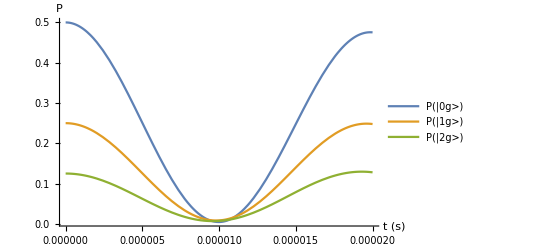

```mathematica
Plot[{Evaluate[ρ[t]/.ρs][[1,2*(n0+1),2*(n0+1)]],Evaluate[ρ[t]/.ρs][[1,2*(n0),2*(n0)]],Evaluate[ρ[t]/.ρs][[1,2*(n0-1),2*(n0-1)]]},{t,0,Ttot},PlotRange->All,PlotLegends->{"P(|0g>)","P(|1g>)","P(|2g>)"},AxesLabel->{"t (s)","P"}]
```

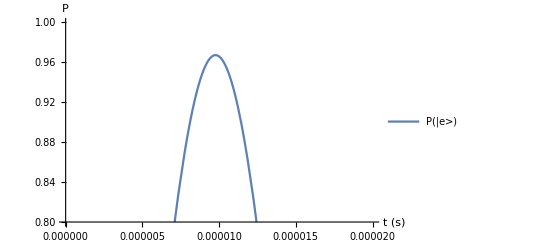

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*n0+1,2}],{t,0,Ttot},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"},PlotRange->{0.8,1.0}]
```

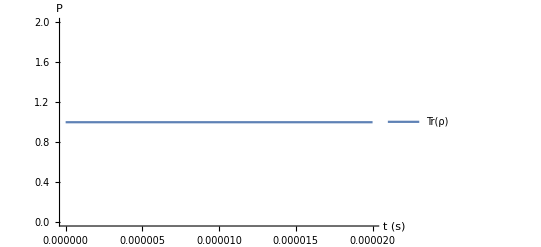

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*(n0+1)}],{t,0,Ttot},PlotLegends->{"Tr(ρ)"},AxesLabel->{"t (s)","P"},PlotRange->All]
```

```mathematica
ρi[2.3965185667708924*^-6]
```

0.990283

```mathematica
1/(2*2.*10^5)
```

2.5×10^-6

```mathematica
tpi=2.3965185667708924*^-6;
nexc=Table[Abs[Evaluate[ρ[tpi]/.ρs][[1,i,i]]],{i,1,7,2}]
```

{0.00215092,0.0139518,0.118834,0.855347}

```mathematica
nexcbar=Sum[(4-n)*nexc[[n]],{n,1,4}]
```

0.15319

```mathematica
nbar=Sum[(n-1)*Pns[[n]],{n,1,4}]
```

0.0999249

### get the pi pulse fidelity for a given Ωc and ωt, set light shift diff to zero

#### fix clock rabi

```mathematica
Ωc=2π 2.0*10^5;
Ttot=1*(2π)/Ωc;
k=(2π)/(578.*10^-9);
```

```mathematica
ωt=2π 5*10.^4;
E0=1/2 ℏ ωt;
v0=√((2E0)/m171);
fdopp=1/(2π)v0*k
```

18201.4

```mathematica
(√(ωR/(2π*10.*10^3)))^6
```

0.0363609

#### vary trap freq

```mathematica
nbar=0.2;
numGrid=50;
ωts=2π Subdivide[1.*10^3,5.*10^4,numGrid-1];
piFidelities=Table[{ωts[[i]]/(2π)*10^-3,0},{i,1,numGrid}];
```

```mathematica
For[ii=1,ii≤numGrid,ii++,
ωt =ωts[[ii]];
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}];
Hn=H/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Abs[Sum[Evaluate[ρ[t] /. ρs][[1,i,i]], {i, 1,2*n0+1, 2}]]},{t,0.,Ttot,Ttot/30}];
piFidelities[[ii,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
Print[ii]
];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

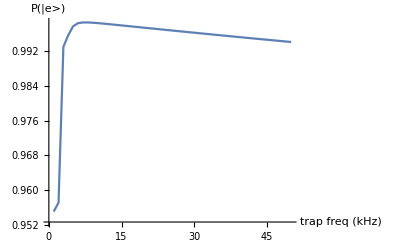

```mathematica
ListPlot[{piFidelities},Joined->True,PlotRange->All,AxesLabel->{"trap freq (kHz)", "P(|e>)"}]
```

```mathematica
piFidelities[[3]]
```

{25.8333,0.996771}

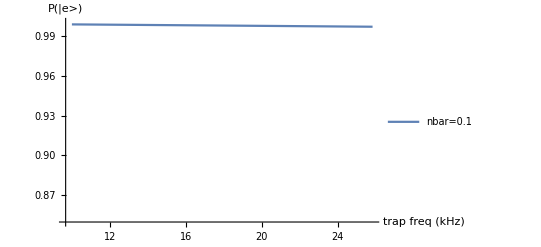

```mathematica
ListPlot[{piFidelities[[1]],piFidelities[[2]],piFidelities[[3]]},Joined->True,PlotRange->{0.85,1.0},AxesLabel->{"trap freq (kHz)", "P(|e>)"},PlotLegends->{StringJoin["nbar=",ToString[nbars[[1]]]],StringJoin["nbar=",ToString[nbars[[2]]]],StringJoin["nbar=",ToString[nbars[[3]]]],StringJoin["nbar=",ToString[nbars[[4]]]],StringJoin["nbar=",ToString[nbars[[5]]]]}]
```

```mathematica
S
```

```mathematica
T0=(ℏ ωt)/(kb Log[1/0.5+1]);
Pns=Table[Pn[n,T0/2],{n,0,3}]
```

{0.888889,0.0987654,0.0109739,0.00121933}

```mathematica
piFidelities[[1,;;,2]]
```

{0.914951,0.869034,0.897427,0.921231,0.93818,0.950378,0.959297,0.966021,0.971195,0.975238,0.978433,0.980981,0.983028,0.984676,0.985999,0.987066,0.987923,0.988605,0.989137,0.989543,0.98984,0.990041,0.990159,0.990202,0.990179,0.990097,0.989961,0.989776,0.989546,0.989275,0.988967,0.988623,0.988246,0.987839,0.987404,0.986941,0.986453,0.985941,0.985407,0.984851,0.984275,0.983679,0.983065,0.982434,0.981786,0.981122,0.980442,0.979749,0.979041,0.97832}

```mathematica
Max[piFidelities[[1,;;,2]]]
```

0.99624

```mathematica
piFidelities[[1,24]]
```

{48.,0.990202}

#### vary trap freq

```mathematica
nbars=Table[i*0.1,{i,1,5}];
numGrid=60;
ωts=2π Subdivide[1.*10^3,2.*10^5,numGrid-1];
piFidelitiesA=Table[{ωts[[i]]/(2π)*10^-3,0},{j,1,Length[nbars]},{i,1,numGrid}];
```

```mathematica
For[jj=1,jj≤Length[nbars],jj++,
For[ii=1,ii≤numGrid,ii++,
ωt =ωts[[ii]];
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}];
Hn=H/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Abs[Sum[Evaluate[ρ[t] /. ρs][[1,i,i]], {i, 1,2*n0+1, 2}]]},{t,0.,Ttot,Ttot/30}];
piFidelitiesA[[jj,ii,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
Print[jj]
]
```

1

2

3

4

5

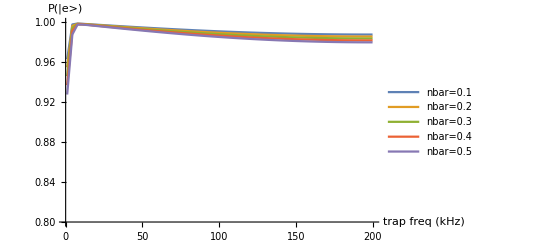

```mathematica
ListPlot[{piFidelitiesA[[1]],piFidelitiesA[[2]],piFidelitiesA[[3]],piFidelitiesA[[4]],piFidelitiesA[[5]]},Joined->True,PlotRange->{0.8,1.0},AxesLabel->{"trap freq (kHz)", "P(|e>)"},PlotLegends->{StringJoin["nbar=",ToString[nbars[[1]]]],StringJoin["nbar=",ToString[nbars[[2]]]],StringJoin["nbar=",ToString[nbars[[3]]]],StringJoin["nbar=",ToString[nbars[[4]]]],StringJoin["nbar=",ToString[nbars[[5]]]]}]
```

```mathematica
T0=(ℏ ωt)/(kb Log[1/0.5+1]);
Pns=Table[Pn[n,T0/2],{n,0,3}]
```

{0.888889,0.0987654,0.0109739,0.00121933}

```mathematica
piFidelities[[1,;;,2]]
```

{0.994972,0.992019,0.989208,0.986597,0.984223,0.982109,0.98029,0.978781,0.977591,0.976731,0.976198,0.975987,0.976088,0.976483,0.977152,0.978065,0.97919,0.980496,0.981948,0.983505,0.985129,0.986782,0.988425,0.990026,0.991553}

```mathematica
Max[piFidelities[[1,;;,2]]]
```

0.99624

```mathematica
piFidelities[[1,24]]
```

{48.,0.990202}

## adiabatic transfer w/ motional dephasing

```mathematica
Ωc=2π 2.*10^5;
ωt=2π 4.8*10^4;
Ttot=(5π)/Ωc;
nbar=0.1;
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
k=(2π)/(578.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
Pns=Table[Pn[n,T0/2],{n,0,n0}]
Pns[[4]]=1-Pns[[3]]-Pns[[2]]-Pns[[1]]
Δadb[t_]:= Δs((2*t)/Tp-1)+Δ0
n0=3;
Hs0a[t_]:=({{-1/2 Δadb[t], Ω/2}, {Ω/2, 1/2 Δadb[t]}});
Hsa[t_]:=KroneckerProduct[IdentityMatrix[n0+1],Hs0a[t]];
Hm:=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ωe, 0}, {0, ωg}})];Hcs=I η Ω/2({{0, 1}, {-1, 0}});
Hcm=({{0, √3, 0, 0}, {√3, 0, √2, 0}, {0, √2, 0, 1}, {0, 0, 1, 0}});
Hc=KroneckerProduct[Hcm,Hcs];
MatrixForm[Hc];
Ha[t_]:=Hsa[t]+Hm+Hc;
MatrixForm[Ha[t]]
```

{0.991736,0.00819616,0.0000677369,5.59809×10^-7}

5.64474×10^-7

(1/2 (-Δ0-(-1+(2 t)/Tp) Δs)+(7 ωe)/2 | Ω/2 | 0 | 1/2 ⅈ √3 η Ω | 0 | 0 | 0 | 0
Ω/2 | 1/2 (Δ0+(-1+(2 t)/Tp) Δs)+(7 ωg)/2 | -1/2 ⅈ √3 η Ω | 0 | 0 | 0 | 0 | 0
0 | 1/2 ⅈ √3 η Ω | 1/2 (-Δ0-(-1+(2 t)/Tp) Δs)+(5 ωe)/2 | Ω/2 | 0 | (ⅈ η Ω)/(√2) | 0 | 0
-1/2 ⅈ √3 η Ω | 0 | Ω/2 | 1/2 (Δ0+(-1+(2 t)/Tp) Δs)+(5 ωg)/2 | -(ⅈ η Ω)/(√2) | 0 | 0 | 0
0 | 0 | 0 | (ⅈ η Ω)/(√2) | 1/2 (-Δ0-(-1+(2 t)/Tp) Δs)+(3 ωe)/2 | Ω/2 | 0 | (ⅈ η Ω)/2
0 | 0 | -(ⅈ η Ω)/(√2) | 0 | Ω/2 | 1/2 (Δ0+(-1+(2 t)/Tp) Δs)+(3 ωg)/2 | -1/2 ⅈ η Ω | 0
0 | 0 | 0 | 0 | 0 | (ⅈ η Ω)/2 | 1/2 (-Δ0-(-1+(2 t)/Tp) Δs)+ωe/2 | Ω/2
0 | 0 | 0 | 0 | -1/2 ⅈ η Ω | 0 | Ω/2 | 1/2 (Δ0+(-1+(2 t)/Tp) Δs)+ωg/2)

```mathematica
Han[t_]:=Ha[t]/.{ωe->ωt/4,ωg->ωt,Ω->Ωc,Δ0->(4ωt)/4,Δs->1.5ωt,η->η0,Tp->Ttot};
ρs=NDSolve[{I ρ'[t]==Han[t].ρ[t]-ρ[t].Han[t],ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
```

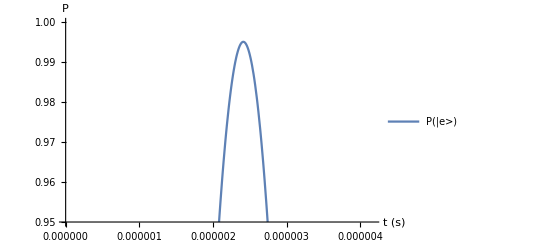

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,7,2}],{t,0,Ttot/3},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"},PlotRange->{0.95,1.0}]
```

```mathematica
1.2*10^6/(2π)
```

190986.

```mathematica
P0=100./2.5;
I0=(2*P0)/(π*(0.6*10^-1)^2)/139
```

50.8889

```mathematica
100./2.5
```

40.

## don’t expand in η

```mathematica
n0=5;
Hs0=({{δ, 0}, {0, 0}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ωe, 0}, {0, ωg}})];
a=DiagonalMatrix[Table[√(n0-n),{n,0,n0}]];
For[i=n0,i>0,i--,
a=Permute[a,Cycles[{{i,i+1}}]]
]
Hcsge=Ω/2({{0, 1}, {0, 0}});
Hcmge=MatrixExp[I η(a+a†)](*IdentityMatrix[n0+1]+Sum[(I η)^n/(n!)MatrixPower[(a+a†),n],{n,1,6}]*);
Hcge=KroneckerProduct[Hcmge,Hcsge];
Hc=Hcge+Hcge†;
H0=Hs+Hm+Hc;
H1=Hs+Hm;
MatrixForm[a];
MatrixForm[Hs];
MatrixForm[Hc];
MatrixForm[Hm];
MatrixForm[H];
```

```mathematica
nbar=1;
T0=(ℏ ωt)/(kb Log[1/nbar+1])
Pns=Table[Pn[n,T0],{n,0,n0}];
ωt=2π *8.*10^3;
Ωc=2π 5*10^4;
Ttot=(2π)/Ωc;
k=(2π)/(578.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}]
```

5.25491×10^-7

0.03125

```mathematica
Hn=H0/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,Ttot/30}];
NMaximize[{ρi[t],{t>0.,t<Ttot}},t]
```

{0.996248,{t→9.98363×10^-6}}

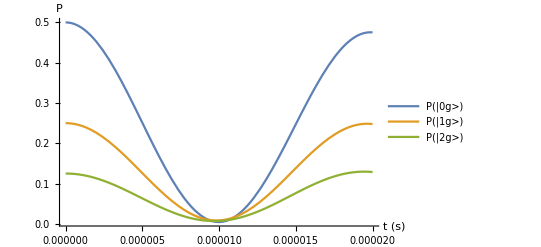

```mathematica
Plot[{Evaluate[ρ[t]/.ρs][[1,2*(n0+1),2*(n0+1)]],Evaluate[ρ[t]/.ρs][[1,2*(n0),2*(n0)]],Evaluate[ρ[t]/.ρs][[1,2*(n0-1),2*(n0-1)]]},{t,0,Ttot},PlotRange->All,PlotLegends->{"P(|0g>)","P(|1g>)","P(|2g>)"},AxesLabel->{"t (s)","P"}]
```

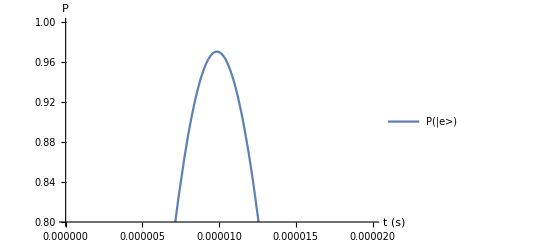

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*n0+1,2}],{t,0,Ttot},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"},PlotRange->{0.8,1.0}]
```

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*(n0+1)}],{t,0,Ttot},PlotLegends->{"Tr(ρ)"},AxesLabel->{"t (s)","P"},PlotRange->All]
```

-Graphics-

```mathematica
Hn0=H0/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
Hn1=H1/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
Hn2=H0/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
ρs0=NDSolve[{I ρ'[t]==Hn0.ρ[t]-ρ[t].Hn0,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi0=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs0][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,Ttot/30}];
```

```mathematica
NMaximize[{ρi0[t],{t>0.,t<Ttot}},t][[1]]
```

0.996248

```mathematica
tpi=NMaximize[{ρi0[t],{t>0.,t<Ttot}},t][[2,1,2]]
```

9.98363×10^-6

```mathematica
Ttot1=10.^-2;
ρf0=Evaluate[ρ[tpi] /. ρs][[1]];
ρs1=NDSolve[{I ρ'[t]==Hn1.ρ[t]-ρ[t].Hn1,ρ[tpi]==ρf0},ρ,{t,tpi,Ttot1+tpi},AccuracyGoal->7];
ρi1=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs1][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,tpi,Ttot1+tpi,Ttot1/300}];
```

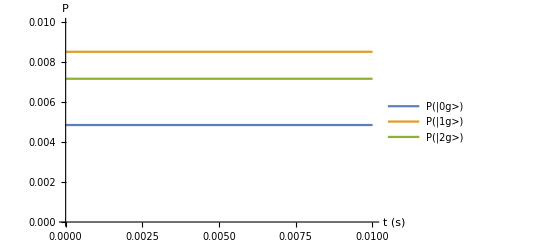

```mathematica
Plot[{Evaluate[ρ[t]/.ρs1][[1,2*(n0+1),2*(n0+1)]],Evaluate[ρ[t]/.ρs1][[1,2*(n0),2*(n0)]],Evaluate[ρ[t]/.ρs1][[1,2*(n0-1),2*(n0-1)]]},{t,tpi,Ttot1+tpi},PlotRange->{0,0.01},PlotLegends->{"P(|0g>)","P(|1g>)","P(|2g>)"},AxesLabel->{"t (s)","P"}]
```

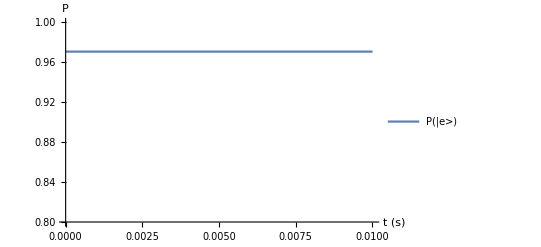

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs1][[1,i,i]],{i,1,2*n0+1,2}],{t,tpi,Ttot1+tpi},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"},PlotRange->{0.8,1.0}]
```

```mathematica
ρf1=Evaluate[ρ[Ttot1+tpi] /. ρs1][[1]];
ρs2=NDSolve[{I ρ'[t]==Hn0.ρ[t]-ρ[t].Hn0,ρ[Ttot1]==ρf1},ρ,{t,Ttot1,Ttot1+Ttot},AccuracyGoal->7];
ρi2=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs2][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,Ttot1,Ttot1+Ttot,Ttot/30}];
```

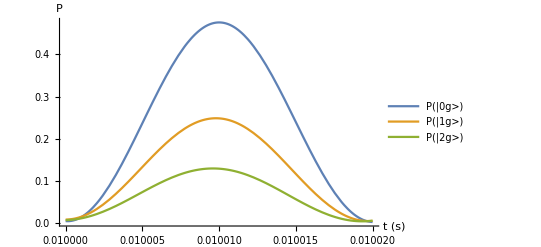

```mathematica
Plot[{Evaluate[ρ[t]/.ρs2][[1,2*(n0+1),2*(n0+1)]],Evaluate[ρ[t]/.ρs2][[1,2*(n0),2*(n0)]],Evaluate[ρ[t]/.ρs2][[1,2*(n0-1),2*(n0-1)]]},{t,Ttot1,Ttot1+Ttot},PlotRange->All,PlotLegends->{"P(|0g>)","P(|1g>)","P(|2g>)"},AxesLabel->{"t (s)","P"}]
```

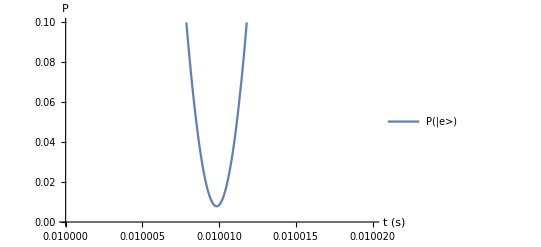

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs2][[1,i,i]],{i,1,2*n0+1,2}],{t,Ttot1,Ttot1+Ttot},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"},PlotRange->{0.0,0.1}]
```

```mathematica
ρf0=Evaluate[ρ[tpi] /. ρs0][[1]];
numF=50;
Tds=Table[ii*4*10^-6,{ii,1,numF}];
pipiFidelity=Table[{Tds[[ii]],0},{ii,1,numF}];
For[ii=1,ii<=numF,ii++,
Ttot1=Tds[[ii]];
ρs1=NDSolve[{I ρ'[t]==Hn1.ρ[t]-ρ[t].Hn1,ρ[tpi]==ρf0},ρ,{t,tpi,Ttot1+tpi},AccuracyGoal->7];
ρi1=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs1][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,tpi,Ttot1+tpi,Ttot1/300}];
ρf1=Evaluate[ρ[Ttot1+tpi] /. ρs1][[1]];
ρs2=NDSolve[{I ρ'[t]==Hn0.ρ[t]-ρ[t].Hn0,ρ[Ttot1]==ρf1},ρ,{t,Ttot1,Ttot1+Ttot},AccuracyGoal->7];
ρi2=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs2][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,Ttot1,Ttot1+Ttot,Ttot/30}];
pipiFidelity[[ii,2]]=1-NMinimize[{ρi2[t],{t>Ttot1,t<Ttot1+Ttot}},t][[1]];
If[Mod[ii,5]==0,Print[ii]]
]
```

5

10

15

20

25

30

35

40

45

50

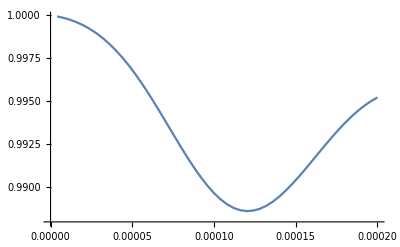

```mathematica
ListPlot[pipiFidelity,Joined->True]
```

```mathematica
ρf0=Evaluate[ρ[tpi] /. ρs0][[1]];
numF=50;
Tds=Table[ii*4*10^-6,{ii,1,numF}];
pipiFidelity=Table[{Tds[[ii]],0},{ii,1,numF}];
For[ii=1,ii<=numF,ii++,
Ttot1=Tds[[ii]];
ρs1=NDSolve[{I ρ'[t]==Hn1.ρ[t]-ρ[t].Hn1,ρ[tpi]==ρf0},ρ,{t,tpi,Ttot1+tpi},AccuracyGoal->7];
ρi1=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs1][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,tpi,Ttot1+tpi,Ttot1/300}];
ρf1=Evaluate[ρ[Ttot1+tpi] /. ρs1][[1]];
ρs2=NDSolve[{I ρ'[t]==Hn0.ρ[t]-ρ[t].Hn0,ρ[Ttot1]==DiagonalMatrix[Flatten[Table[ρf1[[n,n]],{n,1,2*(n0+1)}]]]},ρ,{t,Ttot1,Ttot1+Ttot},AccuracyGoal->7];
ρi2=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs2][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,Ttot1,Ttot1+Ttot,Ttot/30}];
pipiFidelity[[ii,2]]=1-NMaximize[{ρi2[t],{t>Ttot1,t<Ttot1+Ttot}},t][[1]];
If[Mod[ii,5]==0,Print[ii]]
]
```

5

10

15

20

25

30

35

40

45

50

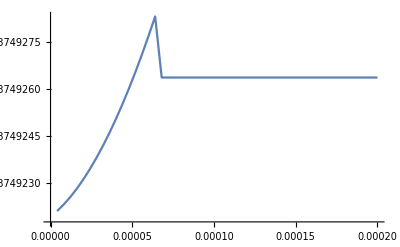

```mathematica
ListPlot[pipiFidelity,Joined->True]
```

#### vary trap freq

```mathematica
nbars=Table[i*0.15+0.05,{i,0,3}];
numGrid=50;
ωts=2π Subdivide[2.*10^4,2.*10^5,numGrid-1];
piFidelities=Table[{ωts[[i]]/(2π)*10^-3,0},{j,1,Length[nbars]},{i,1,numGrid}];
```

```mathematica
For[jj=1,jj≤Length[nbars],jj++,
For[ii=1,ii≤numGrid,ii++,
ωt =ωts[[ii]];
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}];
Hn=H/.{ωe->ωt,ωg->ωt,Ω->Ωc,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Abs[Sum[Evaluate[ρ[t] /. ρs][[1,i,i]], {i, 1,2*n0+1, 2}]]},{t,0.,Ttot,Ttot/30}];
piFidelities[[jj,ii,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
Print[jj]
]
```

1

2

3

4

```mathematica
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/(2π (134*10^3)))
```

0.157237

```mathematica
Pns
```

{0.666667,0.333333}

```mathematica
nbars
```

{0.05,0.2,0.35,0.5}

```mathematica
piFidelities[[2]]
```

{{20.,0.997428},{23.6735,0.997014},{27.3469,0.996603},{31.0204,0.996196},{34.6939,0.995793},{38.3673,0.995395},{42.0408,0.995001},{45.7143,0.994612},{49.3878,0.994229},{53.0612,0.993851},{56.7347,0.993479},{60.4082,0.993114},{64.0816,0.992755},{67.7551,0.992404},{71.4286,0.992059},{75.102,0.991721},{78.7755,0.991392},{82.449,0.99107},{86.1224,0.990756},{89.7959,0.990451},{93.4694,0.990155},{97.1429,0.989867},{100.816,0.989589},{104.49,0.989319},{108.163,0.98906},{111.837,0.98881},{115.51,0.988569},{119.184,0.988336},{122.857,0.988115},{126.531,0.987905},{130.204,0.987705},{133.878,0.987514},{137.551,0.987334},{141.224,0.987165},{144.898,0.987006},{148.571,0.986857},{152.245,0.986719},{155.918,0.986591},{159.592,0.986475},{163.265,0.986369},{166.939,0.986274},{170.612,0.986189},{174.286,0.986115},{177.959,0.986052},{181.633,0.985999},{185.306,0.985956},{188.98,0.985923},{192.653,0.9859},{196.327,0.985889},{200.,0.985887}}

```mathematica
ListPlot[{piFidelities[[1]],piFidelities[[2]],piFidelities[[3]],piFidelities[[4]],piFidelities[[5]]},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"trap frequency (kHz)", "P(|e>)"},PlotLegends->{StringJoin["n=",ToString[nbars[[1]]]],StringJoin["n=",ToString[nbars[[2]]]],StringJoin["n=",ToString[nbars[[3]]]],StringJoin["n=",ToString[nbars[[4]]]],StringJoin["n=",ToString[nbars[[5]]]]},BaseStyle->{FontSize->13},ImageSize->300]
```

ListPlot[{{{20.,0.997919},{23.6735,0.997593},{27.3469,0.99727},{31.0204,0.99695},{34.6939,0.996632},{38.3673,0.996318},{42.0408,0.996008},{45.7143,0.995702},{49.3878,0.9954},{53.0612,0.995102},{56.7347,0.994809},{60.4082,0.994521},{64.0816,0.994239},{67.7551,0.993961},{71.4286,0.99369},{75.102,0.993424},{78.7755,0.993165},{82.449,0.992911},{86.1224,0.992665},{89.7959,0.992425},{93.4694,0.992192},{97.1429,0.991966},{100.816,0.991747},{104.49,0.991535},{108.163,0.991331},{111.837,0.991134},{115.51,0.990945},{119.184,0.99076},{122.857,0.990586},{126.531,0.990421},{130.204,0.990264},{133.878,0.990114},{137.551,0.989974},{141.224,0.989841},{144.898,0.989717},{148.571,0.989602},{152.245,0.989495},{155.918,0.989396},{159.592,0.989305},{163.265,0.989222},{166.939,0.989148},{170.612,0.989083},{174.286,0.989026},{177.959,0.988977},{181.633,0.988937},{185.306,0.988905},{188.98,0.988881},{192.653,0.988866},{196.327,0.988858},{200.,0.988858}},{{20.,0.997428},{23.6735,0.997014},{27.3469,0.996603},{31.0204,0.996196},{34.6939,0.995793},{38.3673,0.995395},{42.0408,0.995001},{45.7143,0.994612},{49.3878,0.994229},{53.0612,0.993851},{56.7347,0.993479},{60.4082,0.993114},{64.0816,0.992755},{67.7551,0.992404},{71.4286,0.992059},{75.102,0.991721},{78.7755,0.991392},{82.449,0.99107},{86.1224,0.990756},{89.7959,0.990451},{93.4694,0.990155},{97.1429,0.989867},{100.816,0.989589},{104.49,0.989319},{108.163,0.98906},{111.837,0.98881},{115.51,0.988569},{119.184,0.988336},{122.857,0.988115},{126.531,0.987905},{130.204,0.987705},{133.878,0.987514},{137.551,0.987334},{141.224,0.987165},{144.898,0.987006},{148.571,0.986857},{152.245,0.986719},{155.918,0.986591},{159.592,0.986475},{163.265,0.986369},{166.939,0.986274},{170.612,0.986189},{174.286,0.986115},{177.959,0.986052},{181.633,0.985999},{185.306,0.985956},{188.98,0.985923},{192.653,0.9859},{196.327,0.985889},{200.,0.985887}},{{20.,0.996939},{23.6735,0.996438},{27.3469,0.99594},{31.0204,0.995447},{34.6939,0.994958},{38.3673,0.994476},{42.0408,0.993999},{45.7143,0.993528},{49.3878,0.993064},{53.0612,0.992607},{56.7347,0.992157},{60.4082,0.991715},{64.0816,0.991281},{67.7551,0.990856},{71.4286,0.990439},{75.102,0.990031},{78.7755,0.989633},{82.449,0.989244},{86.1224,0.988865},{89.7959,0.988497},{93.4694,0.988138},{97.1429,0.98779},{100.816,0.987453},{104.49,0.987127},{108.163,0.986812},{111.837,0.986509},{115.51,0.986217},{119.184,0.985937},{122.857,0.985667},{126.531,0.985411},{130.204,0.985168},{133.878,0.984938},{137.551,0.98472},{141.224,0.984514},{144.898,0.984321},{148.571,0.984141},{152.245,0.983973},{155.918,0.983818},{159.592,0.983675},{163.265,0.983546},{166.939,0.983428},{170.612,0.983324},{174.286,0.983232},{177.959,0.983153},{181.633,0.983087},{185.306,0.983034},{188.98,0.982994},{192.653,0.982964},{196.327,0.982948},{200.,0.982944}},{{20.,0.996463},{23.6735,0.995874},{27.3469,0.99529},{31.0204,0.994711},{34.6939,0.994139},{38.3673,0.993573},{42.0408,0.993014},{45.7143,0.992462},{49.3878,0.991919},{53.0612,0.991383},{56.7347,0.990856},{60.4082,0.990339},{64.0816,0.989831},{67.7551,0.989332},{71.4286,0.988845},{75.102,0.988367},{78.7755,0.987901},{82.449,0.987446},{86.1224,0.987003},{89.7959,0.986571},{93.4694,0.986152},{97.1429,0.985745},{100.816,0.985352},{104.49,0.98497},{108.163,0.984603},{111.837,0.984248},{115.51,0.983906},{119.184,0.983577},{122.857,0.983261},{126.531,0.982962},{130.204,0.982677},{133.878,0.982406},{137.551,0.982149},{141.224,0.981908},{144.898,0.981681},{148.571,0.981468},{152.245,0.981271},{155.918,0.981089},{159.592,0.980921},{163.265,0.980768},{166.939,0.98063},{170.612,0.980507},{174.286,0.980398},{177.959,0.980304},{181.633,0.980224},{185.306,0.98016},{188.98,0.980111},{192.653,0.980075},{196.327,0.980053},{200.,0.980046}},{{{20.,0.997919},{23.6735,0.997593},{27.3469,0.99727},{31.0204,0.99695},{34.6939,0.996632},{38.3673,0.996318},{42.0408,0.996008},{45.7143,0.995702},{49.3878,0.9954},{53.0612,0.995102},{56.7347,0.994809},{60.4082,0.994521},{64.0816,0.994239},{67.7551,0.993961},{71.4286,0.99369},{75.102,0.993424},{78.7755,0.993165},{82.449,0.992911},{86.1224,0.992665},{89.7959,0.992425},{93.4694,0.992192},{97.1429,0.991966},{100.816,0.991747},{104.49,0.991535},{108.163,0.991331},{111.837,0.991134},{115.51,0.990945},{119.184,0.99076},{122.857,0.990586},{126.531,0.990421},{130.204,0.990264},{133.878,0.990114},{137.551,0.989974},{141.224,0.989841},{144.898,0.989717},{148.571,0.989602},{152.245,0.989495},{155.918,0.989396},{159.592,0.989305},{163.265,0.989222},{166.939,0.989148},{170.612,0.989083},{174.286,0.989026},{177.959,0.988977},{181.633,0.988937},{185.306,0.988905},{188.98,0.988881},{192.653,0.988866},{196.327,0.988858},{200.,0.988858}},{{20.,0.997428},{23.6735,0.997014},{27.3469,0.996603},{31.0204,0.996196},{34.6939,0.995793},{38.3673,0.995395},{42.0408,0.995001},{45.7143,0.994612},{49.3878,0.994229},{53.0612,0.993851},{56.7347,0.993479},{60.4082,0.993114},{64.0816,0.992755},{67.7551,0.992404},{71.4286,0.992059},{75.102,0.991721},{78.7755,0.991392},{82.449,0.99107},{86.1224,0.990756},{89.7959,0.990451},{93.4694,0.990155},{97.1429,0.989867},{100.816,0.989589},{104.49,0.989319},{108.163,0.98906},{111.837,0.98881},{115.51,0.988569},{119.184,0.988336},{122.857,0.988115},{126.531,0.987905},{130.204,0.987705},{133.878,0.987514},{137.551,0.987334},{141.224,0.987165},{144.898,0.987006},{148.571,0.986857},{152.245,0.986719},{155.918,0.986591},{159.592,0.986475},{163.265,0.986369},{166.939,0.986274},{170.612,0.986189},{174.286,0.986115},{177.959,0.986052},{181.633,0.985999},{185.306,0.985956},{188.98,0.985923},{192.653,0.9859},{196.327,0.985889},{200.,0.985887}},{{20.,0.996939},{23.6735,0.996438},{27.3469,0.99594},{31.0204,0.995447},{34.6939,0.994958},{38.3673,0.994476},{42.0408,0.993999},{45.7143,0.993528},{49.3878,0.993064},{53.0612,0.992607},{56.7347,0.992157},{60.4082,0.991715},{64.0816,0.991281},{67.7551,0.990856},{71.4286,0.990439},{75.102,0.990031},{78.7755,0.989633},{82.449,0.989244},{86.1224,0.988865},{89.7959,0.988497},{93.4694,0.988138},{97.1429,0.98779},{100.816,0.987453},{104.49,0.987127},{108.163,0.986812},{111.837,0.986509},{115.51,0.986217},{119.184,0.985937},{122.857,0.985667},{126.531,0.985411},{130.204,0.985168},{133.878,0.984938},{137.551,0.98472},{141.224,0.984514},{144.898,0.984321},{148.571,0.984141},{152.245,0.983973},{155.918,0.983818},{159.592,0.983675},{163.265,0.983546},{166.939,0.983428},{170.612,0.983324},{174.286,0.983232},{177.959,0.983153},{181.633,0.983087},{185.306,0.983034},{188.98,0.982994},{192.653,0.982964},{196.327,0.982948},{200.,0.982944}},{{20.,0.996463},{23.6735,0.995874},{27.3469,0.99529},{31.0204,0.994711},{34.6939,0.994139},{38.3673,0.993573},{42.0408,0.993014},{45.7143,0.992462},{49.3878,0.991919},{53.0612,0.991383},{56.7347,0.990856},{60.4082,0.990339},{64.0816,0.989831},{67.7551,0.989332},{71.4286,0.988845},{75.102,0.988367},{78.7755,0.987901},{82.449,0.987446},{86.1224,0.987003},{89.7959,0.986571},{93.4694,0.986152},{97.1429,0.985745},{100.816,0.985352},{104.49,0.98497},{108.163,0.984603},{111.837,0.984248},{115.51,0.983906},{119.184,0.983577},{122.857,0.983261},{126.531,0.982962},{130.204,0.982677},{133.878,0.982406},{137.551,0.982149},{141.224,0.981908},{144.898,0.981681},{148.571,0.981468},{152.245,0.981271},{155.918,0.981089},{159.592,0.980921},{163.265,0.980768},{166.939,0.98063},{170.612,0.980507},{174.286,0.980398},{177.959,0.980304},{181.633,0.980224},{185.306,0.98016},{188.98,0.980111},{192.653,0.980075},{196.327,0.980053},{200.,0.980046}}}⟦5⟧},Joined→True,PlotRange→All,Frame→True,FrameLabel→{trap frequency (kHz),P(|e>)},PlotLegends→{n=0.05,n=0.2,n=0.35,n=0.5,n={0.05, 0.2, 0.35, 0.5}[[5]]},BaseStyle→{FontSize→13},ImageSize→300]

```mathematica
√(0.3/5.84)*140
```

31.7309

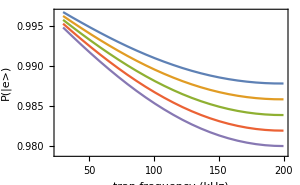
```mathematica
Export["C:\\Users\\alecj\\JILA\\Analysis_code_Yb\\Yb_notebooks\\atom_calculations\\clock_dephasing.pdf", -Graphics-]
```

C:\Users\alecj\JILA\Analysis_code_Yb\Yb_notebooks\atom_calculations\clock_dephasing.pdf

```mathematica
piInfidelities=Table[Transpose[{piFidelities[[i,;;,1]],1-piFidelities[[i,;;,2]]}],{i,1,Length[piFidelities]}];
For[jj=1,jj≤Length[piInfidelities],jj++,
Export["C:/Users/alecj/JILA/papers/Yb171Qubit/calculations/clock_dephasing"<>ToString[jj]<>".txt",piInfidelities[[jj]],"CSV"]
]
Export["C:/Users/alecj/JILA/papers/Yb171Qubit/calculations/nbars.txt",nbars,"CSV"]
```

C:/Users/alecj/JILA/papers/Yb171Qubit/calculations/nbars.txt

C:/Users/alecj/JILA/papers/Yb171Qubit/calculations/nbars.txt

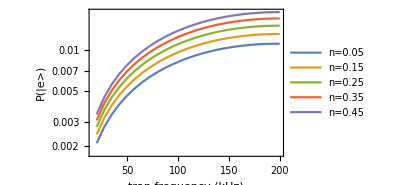

```mathematica
ListLogPlot[{piInfidelities[[1]],piInfidelities[[2]],piInfidelities[[3]],piInfidelities[[4]],piInfidelities[[5]]},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"trap frequency (kHz)", "P(|e>)"},PlotLegends->{StringJoin["n=",ToString[nbars[[1]]]],StringJoin["n=",ToString[nbars[[2]]]],StringJoin["n=",ToString[nbars[[3]]]],StringJoin["n=",ToString[nbars[[4]]]],StringJoin["n=",ToString[nbars[[5]]]]},BaseStyle->{FontSize->13},ImageSize->300]
```

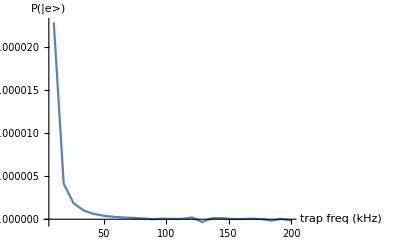

```mathematica
ListPlot[dpiFidelities,Joined->True,PlotRange->All,AxesLabel->{"trap freq (kHz)", "P(|e>)"}]
```

```mathematica
T0=(ℏ ωt)/(kb Log[1/0.5+1]);
Pns=Table[Pn[n,T0/2],{n,0,3}]
```

{0.888889,0.0987654,0.0109739,0.00121933}

```mathematica
piFidelities[[1,;;,2]]
```

{0.994995,0.992023,0.98921,0.986598,0.984223,0.98211,0.980291,0.978782,0.977592,0.976731,0.976198,0.975987,0.976088,0.976483,0.977152,0.978064,0.97919,0.980497,0.981948,0.983505,0.985129,0.986782,0.988425,0.990026,0.991553}

```mathematica
Max[piFidelities[[1,;;,2]]]
```

0.99624

```mathematica
piFidelities[[1,24]]
```

{48.,0.990202}